```mathematica
HH={{0,Exp[-I*θ],Exp[I*θ]},{Exp[I*θ],0,0},{Exp[-I*θ],0,0}} + {{a,0,0},{0,-a,0},{0,0,-a}};
```

```mathematica
MatrixForm[{{a,ⅇ^(-ⅈ θ),ⅇ^(ⅈ θ)},{ⅇ^(ⅈ θ),-a,0},{ⅇ^(-ⅈ θ),0,-a}}]
```

(a | ⅇ^(-ⅈ θ) | ⅇ^(ⅈ θ)
ⅇ^(ⅈ θ) | -a | 0
ⅇ^(-ⅈ θ) | 0 | -a)

```mathematica
MatrixForm[{{a,ⅇ^(ⅈ θ),ⅇ^(-ⅈ θ)},{ⅇ^(-ⅈ θ),-a,0},{ⅇ^(ⅈ θ),0,-a}}]
```

(a | ⅇ^(ⅈ θ) | ⅇ^(-ⅈ θ)
ⅇ^(-ⅈ θ) | -a | 0
ⅇ^(ⅈ θ) | 0 | -a)

```mathematica
FullSimplify[Eigensystem[HH]]
```

{{-a,-√(2+a^2),√(2+a^2)},{{0,-ⅇ^(2 ⅈ θ),1},{(a-√(2+a^2)) ⅇ^(ⅈ θ),ⅇ^(2 ⅈ θ),1},{(a+√(2+a^2)) ⅇ^(ⅈ θ),ⅇ^(2 ⅈ θ),1}}}

```mathematica
MatrixForm[{{1,ⅇ^(ⅈ θ),ⅇ^(-ⅈ θ)},{ⅇ^(-ⅈ θ),-1,0},{ⅇ^(ⅈ θ),0,-1}}]
```

(1 | ⅇ^(ⅈ θ) | ⅇ^(-ⅈ θ)
ⅇ^(-ⅈ θ) | -1 | 0
ⅇ^(ⅈ θ) | 0 | -1)

```mathematica
TableForm[{{1,ⅇ^(ⅈ θ),ⅇ^(-ⅈ θ)},{ⅇ^(-ⅈ θ),-1,0},{ⅇ^(ⅈ θ),0,-1}}]
```

1 | ⅇ^(ⅈ θ) | ⅇ^(-ⅈ θ)
ⅇ^(-ⅈ θ) | -1 | 0
ⅇ^(ⅈ θ) | 0 | -1

```mathematica
MatrixForm[{{1,ⅇ^(ⅈ θ),ⅇ^(-ⅈ θ)},{ⅇ^(-ⅈ θ),-1,0},{ⅇ^(ⅈ θ),0,-1}}]
```

(1 | ⅇ^(ⅈ θ) | ⅇ^(-ⅈ θ)
ⅇ^(-ⅈ θ) | -1 | 0
ⅇ^(ⅈ θ) | 0 | -1)

```mathematica
MatrixForm[{{1,ⅇ^(ⅈ θ),ⅇ^(-ⅈ θ)},{ⅇ^(-ⅈ θ),-1,0},{ⅇ^(ⅈ θ),0,-1}}]
```

(1 | ⅇ^(ⅈ θ) | ⅇ^(-ⅈ θ)
ⅇ^(-ⅈ θ) | -1 | 0
ⅇ^(ⅈ θ) | 0 | -1)

```mathematica
H={{0,Exp[I*θ],Exp[I*θ]},{Exp[-I*θ],0,0},{Exp[-I*θ],0,0}} + {{a,0,0},{0,-a,0},{0,0,-a}};
```

```mathematica
MatrixForm[{{a,ⅇ^(ⅈ θ),ⅇ^(ⅈ θ)},{ⅇ^(-ⅈ θ),-a,0},{ⅇ^(-ⅈ θ),0,-a}}]
FullSimplify[Eigensystem[H]]
```

(a | ⅇ^(ⅈ θ) | ⅇ^(ⅈ θ)
ⅇ^(-ⅈ θ) | -a | 0
ⅇ^(-ⅈ θ) | 0 | -a)

{{-a,-√(2+a^2),√(2+a^2)},{{0,-1,1},{(a-√(2+a^2)) ⅇ^(ⅈ θ),1,1},{(a+√(2+a^2)) ⅇ^(ⅈ θ),1,1}}}

```mathematica
MatrixForm[{{a,ⅇ^(ⅈ θ),ⅇ^(ⅈ θ)},{ⅇ^(-ⅈ θ),-a,0},{ⅇ^(-ⅈ θ),0,-a}}]
```

(a | ⅇ^(ⅈ θ) | ⅇ^(ⅈ θ)
ⅇ^(-ⅈ θ) | -a | 0
ⅇ^(-ⅈ θ) | 0 | -a)

```mathematica
H2={{0,Exp[I*θ],Exp[-I*θ]},{Exp[-I*θ],0,0},{Exp[I*θ],0,0}} + {{a,0,0},{0,-a,0},{0,0,-a}};
```

```mathematica
MatrixForm[{{a,ⅇ^(ⅈ θ),ⅇ^(-ⅈ θ)},{ⅇ^(-ⅈ θ),-a,0},{ⅇ^(ⅈ θ),0,-a}}]
FullSimplify[Eigensystem[H2]]
```

(a | ⅇ^(ⅈ θ) | ⅇ^(-ⅈ θ)
ⅇ^(-ⅈ θ) | -a | 0
ⅇ^(ⅈ θ) | 0 | -a)

{{-a,-√(2+a^2),√(2+a^2)},{{0,-ⅇ^(-2 ⅈ θ),1},{(a-√(2+a^2)) ⅇ^(-ⅈ θ),ⅇ^(-2 ⅈ θ),1},{(a+√(2+a^2)) ⅇ^(-ⅈ θ),ⅇ^(-2 ⅈ θ),1}}}

```mathematica
MatrixForm[{{a,ⅇ^(ⅈ θ),ⅇ^(-ⅈ θ)},{ⅇ^(ⅈ θ),-a,0},{ⅇ^(-ⅈ θ),0,-a}}]
```

(a | ⅇ^(ⅈ θ) | ⅇ^(-ⅈ θ)
ⅇ^(ⅈ θ) | -a | 0
ⅇ^(-ⅈ θ) | 0 | -a)

```mathematica
H3={{0,b*Exp[-I*θ],b*Exp[I*θ]},{b*Exp[I*θ],0,0},{b*Exp[-I*θ],0,0}} + {{a,0,0},{0,-a,0},{0,0,-a}};
```

```mathematica
FullSimplify[Eigensystem[H3]]
```

{{-a,-√(a^2+2 b^2),√(a^2+2 b^2)},{{0,-ⅇ^(2 ⅈ θ),1},{((a-√(a^2+2 b^2)) ⅇ^(ⅈ θ))/b,ⅇ^(2 ⅈ θ),1},{((a+√(a^2+2 b^2)) ⅇ^(ⅈ θ))/b,ⅇ^(2 ⅈ θ),1}}}

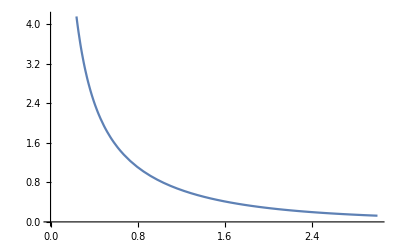

```mathematica
Plot[NIntegrate[r*BesselJ[1,a*r]*Tanh[r]/r,{r,0,∞}],{a,0,3}]
```